```mathematica
(* ===Genesis Closure Toy Model:Fresh Notebook===*)(*Central guess and scan range for ng*)CosmoMisfit[ng_?NumericQ]:=(ng-1.15414)^2+10^-6;
;
ngRange=0.0005;   (*+/-5e-4 around center*)
ngMin=ngCenter-ngRange;
ngMax=ngCenter+ngRange;

(*Map ng->alpha*)
ClearAll[alphaOf];
alphaOf[ng_]:=ng^2-1;
```

```mathematica
(*Layer-preferred ng values*)ngEFTTarget=1.1539800017415;       (*EFT layer prefers this*)
ngCosmoTarget=1.15428;               (*cosmology/closure layer*)
ngObsTarget=1.154307344136304;     (*observer-window layer*)
```

```mathematica
ClearAll[CEFT,Ccosmo,Cobs];

(*Simple quadratic penalties around each target*)
CEFT[ng_]:=(ng-ngEFTTarget)^2;
Ccosmo[ng_]:=(ng-ngCosmoTarget)^2;
Cobs[ng_]:=(ng-ngObsTarget)^2;
```

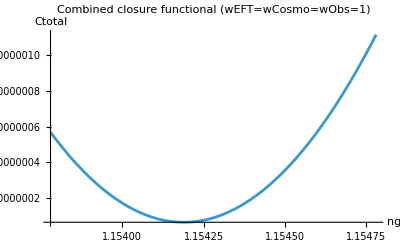

{1.15419,6.59688×10^-8}

```mathematica
ClearAll[Ctotal];

(*Baseline weights:treat all layers equally*)
wEFT=1.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

(*Visualize combined cost in the band*)
baselinePlot=Plot[Ctotal[ng],{ng,ngMin,ngMax},PlotRange->All,AxesLabel->{"ng","Ctotal"},PlotLabel->"Combined closure functional (wEFT=wCosmo=wObs=1)"];

baselinePlot

(*Find minimizing ng in this band*)
baselineMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarBase=ng/. Last[baselineMin];
costStarBase=First[baselineMin];

{ngStarBase,costStarBase}
```

```mathematica
(* ===EFT-heavy case===*)wEFT=3.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

eftMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarEFT=ng/. Last[eftMin];
costStarEFT=First[eftMin];

{ngStarEFT,costStarEFT}

(* ===Observer-heavy case===*)
wEFT=1.0;
wCosmo=1.0;
wObs=3.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

obsMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarObs=ng/. Last[obsMin];
costStarObs=First[obsMin];

{ngStarObs,costStarObs}
```

{1.15411,1.18443×10^-7}

{1.15424,8.27403×10^-8}

```mathematica
resultsTable={{"Case","wEFT","wCosmo","wObs","ng*","Ctotal(ng*)"},{"Baseline",1.0,1.0,1.0,ngStarBase,costStarBase},{"EFT-heavy",3.0,1.0,1.0,ngStarEFT,costStarEFT},{"Observer-heavy",1.0,1.0,3.0,ngStarObs,costStarObs}};

Grid[resultsTable,Frame->All]
```

Case | wEFT | wCosmo | wObs | ng* | Ctotal(ng*)
Baseline | 1. | 1. | 1. | 1.15414 | 1.05359×10^-6
EFT-heavy | 3. | 1. | 1. | 1.15421 | 1.08621×10^-6
Observer-heavy | 1. | 1. | 3. | 1.15408 | 1.08525×10^-6